#### January 20, 2022 For AJP. This goes back to two hollow spheres. Plot of interaction energy, and the combined electric field vectors for locations where both EFields are non zero.

```mathematica
ClearAll["Global`*"]
a = 1.0 10^-3;
rSphere1 = a;
rSphere2 = rSphere1;
dSphere = 4.0 a;   (* Distance between center points of the two spheres *) 
q1 =  10^-12;
q2 = q1;
eps0= 8.85 * 10^-12; 
JoulesToEV = 6.2415093433 * 10^18;
numElements = 25;
xList = Table[(2. + i/2 )a, {i,0, numElements}];
potentialList = Table[{0,0}, {i,0, numElements}];
x2 = dSphere;
x1 = 0.0;
```

#### First, the enclosed charge is just 0 for r<a, and then q1 for r>a. From there the Efield is easy, and then integrate that out to infinity. Then can find the constant of integration, such that the potential at r = ∞ is zero. Then can find potential as a function of distance from the sphere with infinity as the zero reference.

```mathematica
(*  eField1[x_, y_, z_] := qEnclosed1[x, y, z]/(4 π r^2 eps0);   *)
```

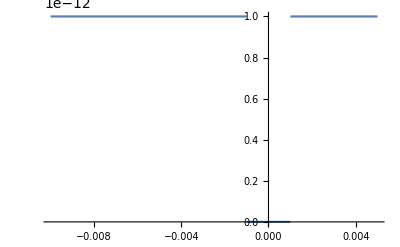

```mathematica
r1[x_, y_, z_] := Norm[{(x-x1), y, z}];  (*  Distance from {x1, 0, 0}  *)
qEnclosed1[x_, y_, z_]:= If[ r1[x, y, z]<= rSphere1, 0., q1];
eMag1[x_, y_, z_] := qEnclosed1[x, y, z]/(4 π eps0( (x-x1)^2 +y^2 + z^2)) ;
eFieldCart1[x_, y_, z_] := eMag1[x, y, z] { (x-x1)/Sqrt[(x-x1)^2 +y^2 +  z^2], y/Sqrt[(x-x1)^2 +y^2+  z^2 ],  z/Sqrt[(x-x1)^2 +y^2+  z^2 ]};
Plot[qEnclosed1[x, 0, 0], {x, -10a, 5a}]
```

```mathematica
r2[x_, y_, z_] := Norm[{(x-x2), y, z}];  (*  Distance from {x1, 0, 0}  *)
qEnclosed2[x_, y_, z_]:= If[Norm[{(x-x2), y, z}] <= rSphere2, 0., q2];
eMag2[x_, y_, z_] := qEnclosed2[x, y, z]/(4 π eps0(( x - x2)^2 +y^2 + z^2)) ;
eFieldCart2[x_, y_, z_] := eMag2[x, y, z] { (x-x2)/Sqrt[(x-x2)^2 +y^2 +  z^2], y/Sqrt[(x-x2)^2 +y^2+  z^2 ],  z/Sqrt[(x-x2)^2 +y^2+  z^2 ]};
```

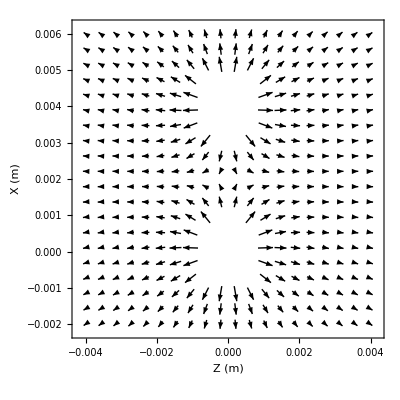

```mathematica
xColumns = 20;
xRange = 2. dSphere;
DeltaX = xRange/(xColumns-1);
X0 = -xRange / 4.0;
XNow = X0;

zRange = xRange;
zRows = xColumns;
DeltaZ = zRange/(zRows-1);
Z0 = -zRange / 2.0;
ZNow = Z0;


oneList = Table[{{i, i}, {2 i, -2 i}}, {i, 1, xColumns*zRows}];
eFieldCartTot[x_, y_, z_] := eFieldCart1[x, y, z] + eFieldCart2[x, y, z] ;
listNum = 0;
For[i=1, i<xColumns+1,i++, 
For[j=1, j<zRows+1,j++, 
listNum++;
oneList[[listNum]][[1]][[1]] = ZNow ;
oneList[[listNum]][[1]][[2]] = XNow ;
(* oneList[[listNum]][[2]][[1]] =  eFieldCart1[XNow, 0., ZNow][[3]]+ eFieldCart2[XNow, 0., ZNow][[3]];
oneList[[listNum]][[2]][[2]] =  eFieldCart1[XNow, 0., ZNow][[1]]+ eFieldCart2[XNow, 0., ZNow][[1]]; *)
Flag1 = 1.0;  (* Flag1 and Flag2 used to suppress printing vectors inside either sphere  *)
Flag2 = 1.0;
If[Norm[{(XNow-x1), 0., ZNow}] <= rSphere1,Flag1 = 0., {}];
If[Norm[{(XNow-x2), 0., ZNow}] <= rSphere2,Flag2 = 0., {}];
oneList[[listNum]][[2]][[1]] =  Flag1 Flag2 eFieldCartTot[XNow, 0., ZNow][[3]];

oneList[[listNum]][[2]][[2]] =  Flag1 Flag2 eFieldCartTot[XNow, 0., ZNow][[1]];
ZNow  = Z0 + DeltaZ (j);
];
XNow  = X0 + DeltaX (i);
ZNow = Z0;
]
Plot1 = ListVectorPlot[oneList, DataRange-> { {Z0, Z0 + DeltaZ*(zRows-1)}, {X0, X0 + DeltaX*(xColumns-1)} }, VectorPoints->All, VectorScaling->"Sqrt",VectorSizes->{0, 1.0},VectorColorFunction->None, VectorStyle-> Black,FrameLabel-> {"Z (m)","X (m)"}, LabelStyle->Directive[Black, FontSize -> 14]]
```

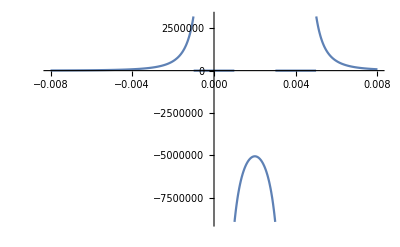

```mathematica
interactionEnergy[x_, y_, z_] := Dot[eFieldCart1[x, y, z],eFieldCart2[x, y, z] ];
Plot[interactionEnergy[x, 0., 0.], {x, -xRange, xRange  },PlotRange->All ]
```

```mathematica
Plot4 = DensityPlot[ interactionEnergy[x,0., z]* 10^-6,   {z,-4.0 rSphere1, 4.0rSphere1}, {x, x1 - 2.0*rSphere1, x2 + 2.0rSphere1 },

PlotRange->All, Exclusions->None, ColorFunction->"Rainbow", PlotPoints->100,

FrameTicks->  {    {{#, #  1000}&/@FindDivisions[{-0.002,0.006},7] //N, Automatic},{{#,1000 #}&/@FindDivisions[{-0.004,0.004},5] //N,Automatic}   }  , 
LabelStyle->Directive[Black, FontSize -> 14],

Frame -> True,  FrameLabel -> {"z (mm)", "x (mm)"}, PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->"w_int (J/cm^3)"],{After,Center}] ]
```

-Graphics-

```mathematica
Show[ Plot4,Plot1]
```